# Open XXZ chain: sectors, eigenstate entropies, and edge evolution

Evaluate definitions 1–2 once. The sweep (3–4) and evolution (5–7) have independent parameters and diagonalizations. Execution is split into editable cells.

## 1. Physics definitions

### Hamiltonian and numerical utilities

Open chain, total size L. S=σ/2, ℏ=1. H=J Σⱼ(SˣⱼSˣⱼ₊₁+SʸⱼSʸⱼ₊₁+ΔSᶻⱼSᶻⱼ₊₁)+h ΣⱼSᶻⱼ+bLeft Sᶻ₁+bRight SᶻL. The system is {1,L}; the environment is {2,…,L−1}. J is signed.

```mathematica
ClearAll[check,realQ,id,maxAbs,herm,ketRho,siteOp,bondOp,xxzH,
 partitionFactor,reducedState,reducedKet,edgeRho,entropy,halfEntropy,edgeEntropy,
 traceA,traceB,ptB,negativity,concurrence,productKet,neel,helix,stateFactor,joinStates,
 charges,splitCharge,fixSign,diagonalizeBlock,sectorED,eigenket,groundKet,
 addEntropies,sweepLabels,packSweep,sweepPoint,sameSpectrum,sectorTable,
 makeEngine,evolve,evolveBatch,observables,timeChunk,timeGrid,startKernels,
 sweepParallel,evolveChunks];
```

```mathematica
(* Stop the current cell if an input or validation fails. *)
check[test_,message_] := If[!TrueQ[test],Print[Style[message,Red ]];Abort[]];
realQ[x_] := NumericQ[x] && NumberQ[N[x ]] && TrueQ[Im[N[x ]]==0];
id[n_] := SparseArray[Band[{1,1}]->1,{n,n}];
maxAbs[a_] := If[Head[a]===SparseArray,
 Max[0,Sequence@@Abs[a["NonzeroValues"]]],Max[0,Sequence@@Abs[Flatten[a ]]]];
herm[a_] := (a+ConjugateTranspose[a])/2;
ketRho[v_] := Outer[Times,v,Conjugate[v ]];
```

```mathematica
(* Embed a one-spin or nearest-neighbour operator. *)
siteOp[a_,k_,l_] := KroneckerProduct[id[2^(k-1)],SparseArray[a],id[2^(l-k)]];
bondOp[a_,b_,k_,l_] := KroneckerProduct[
 id[2^(k-1)],SparseArray[a],SparseArray[b],id[2^(l-k-1)]];
```

```mathematica
(* Full open-chain XXZ Hamiltonian. *)
xxzH[p_Association] := Module[{l=p["L"],d=p["Delta"],h,x,y,z},
 check[IntegerQ[l] && l>=3,"L must be an integer >=3."];
 check[AllTrue[Lookup[p,{"J","Delta","h","bLeft","bRight"}],realQ],
  "J, Delta and fields must be finite real numbers."];
 {x,y,z}=Table[PauliMatrix[k]/2,{k,3}]; h=SparseArray[{}, {2^l,2^l}];
 Do[h+=p["J"](bondOp[x,x,k,l]+bondOp[y,y,k,l]+d bondOp[z,z,k,l]),{k,l-1}];
 Do[h+=p["h"] siteOp[z,k,l],{k,l}];
 SparseArray[h+p["bLeft"] siteOp[z,1,l]+p["bRight"] siteOp[z,l,l ]]
];
```

### Reduced density matrix

```mathematica
(* Coefficient matrix for a chosen set of sites; rho=A.A†. *)
partitionFactor[fac_,sites_List,l_Integer] := Module[{r=Dimensions[fac][[2]],rest},
 rest=Complement[Range[l],sites];
 ArrayReshape[Transpose[ArrayReshape[fac,Join[ConstantArray[2,l],{r}]],
  Ordering[Join[sites,rest,{l+1}]]],{2^Length[sites],2^Length[rest] r}]
];
reducedState[fac_,sites_List,l_Integer] := With[{a=partitionFactor[fac,sites,l]},
 a . ConjugateTranspose[a ]];
reducedKet[v_,sites_List,l_Integer] := reducedState[Transpose[{v}],sites,l];
edgeRho[v_,l_Integer] := reducedKet[v,{1,l},l];
```

```mathematica
(* Single-edge reductions, in edge basis {00,01,10,11}. *)
traceB[r_] := {{r[[1,1]]+r[[2,2]],r[[1,3]]+r[[2,4]]},
 {r[[3,1]]+r[[4,2]],r[[3,3]]+r[[4,4]]}};
traceA[r_] := {{r[[1,1]]+r[[3,3]],r[[1,2]]+r[[3,4]]},
 {r[[2,1]]+r[[4,3]],r[[2,2]]+r[[4,4]]}};
```

### Entanglement computations

```mathematica
(* Von Neumann entropy, natural logarithms. *)
entropy[r_] := Module[{e=Select[Re[Eigenvalues[N[herm[r ]]]],#>0&]},
 If[e==={},0.,-Total[e Log[e ]]]];

(* Pure-state entropy for sites 1,...,floor(L/2). *)
halfEntropy[v_,l_] := Module[{p},
 p=Select[SingularValueList[ArrayReshape[v,{2^Floor[l/2],2^Ceiling[l/2]}]]^2,#>0&];
 If[p==={},0.,-Total[p Log[p ]]]];

(* Pure-state entanglement of both edges together versus the middle. *)
edgeEntropy[v_,l_] := entropy[edgeRho[v,l ]];
```

```mathematica
(* Negativity between spin 1 and spin L. *)
ptB[r_] := ArrayReshape[Transpose[ArrayReshape[r,{2,2,2,2}],{1,4,3,2}],{4,4}];
negativity[r_] := Total[Clip[-Re[Eigenvalues[herm[ptB[r ]]]],{0,Infinity}]];

(* Concurrence from an exact reduced-state factor; stable at rank deficiency. *)
concurrence[a_] := Module[{q,r,f,s},
 {q,r}=QRDecomposition[ConjugateTranspose[a ]]; f=ConjugateTranspose[r];
 s=PadRight[Reverse[Sort[SingularValueList[
  Transpose[f] . KroneckerProduct[PauliMatrix[2],PauliMatrix[2]] . f,Tolerance->0]]],4];
 Max[0.,First[s]-Total[Rest[s ]]]
];
```

### Initial states construction

```mathematica
(* Tensor product of normalized local spinors. *)
productKet[locals_List] := Module[{v},
 check[Length[locals]>0 && AllTrue[locals,
  VectorQ[#,NumericQ] && Length[#]==2 && Norm[#]>0&],"Invalid local spinor."];
 v=Fold[Flatten[KroneckerProduct[#1,N[#2/Norm[#2 ]]]]&,{1.},locals]; v/Norm[v]
];

(* first=0 starts with up; first=1 starts with down. *)
neel[n_Integer,first_:0] := productKet[Table[UnitVector[2,1+Mod[k-1+first,2]],{k,n}]];
(* phi is the azimuth of the first spin in this vector. *)
helix[n_Integer,q_,theta_:Pi/2,phi_:0] := productKet[
 Table[{Cos[theta/2],Exp[I(phi+(k-1)q)] Sin[theta/2]},{k,n}]];
```

```mathematica
(* Accept a vector or a positive, trace-one density matrix. *)
stateFactor[input_,dim_,tol_] := Module[{x=N[Normal[input ]],e,v,keep},
 If[VectorQ[x,NumericQ],check[Length[x]==dim && Norm[x]>0,"Invalid state vector."];
  Return[Transpose[{x/Norm[x]}]]];
 check[MatrixQ[x,NumericQ] && Dimensions[x]=={dim,dim},"Invalid density-matrix dimensions."];
 check[Norm[x-ConjugateTranspose[x],"Frobenius"]<=tol && Abs[Tr[x]-1]<=tol,
  "Density matrix must be Hermitian with trace one."];
 {e,v}=Eigensystem[herm[x ]];check[Min[Re[e ]]>=-tol,"Density matrix is not positive."];
 e=Clip[Re[e],{0,Infinity}];e/=Total[e];keep=Select[Range[dim],e[[# ]]>0&];
 Transpose[Sqrt[e[[keep ]]] v[[keep ]]]
];
(* Reorder (edge 1,edge L,middle) to physical sites 1,...,L. *)
joinStates[ef_,mf_,l_] := Module[{a=KroneckerProduct[ef,mf]},
 ArrayReshape[Transpose[ArrayReshape[a,{2,2,2^(l-2),Dimensions[a][[2]]}],
  {1,3,2,4}],{2^l,Dimensions[a][[2]]}]
];
```

### Basis adaptation respecting symmetries

```mathematica
(* Charges allowed by the effective longitudinal fields. *)
charges[p_] := Module[{l=p["L"],d=2^p["L"],r,f,fields,out=<||>,st,sx,sy,sz},
 fields=ConstantArray[p["h"],l];fields[[1]]+=p["bLeft"];fields[[-1]]+=p["bRight"];
 r=SparseArray[Table[{1+FromDigits[Reverse[IntegerDigits[k,2,l ]],2],k+1}->1,
  {k,0,d-1}],{d,d}];
 f=SparseArray[Table[{d-k,k+1}->1,{k,0,d-1}],{d,d}];
 If[And@@MapThread[TrueQ[#1==#2]&,{fields,Reverse[fields]}],AssociateTo[out,"R"->r ]];
 If[And@@(TrueQ[#==0]& /@ fields),AssociateTo[out,"F"->f ]];
 If[And@@MapThread[TrueQ[#1 == -#2]&,{fields,Reverse[fields]}] &&
  !(KeyExistsQ[out,"R"] && KeyExistsQ[out,"F"]),AssociateTo[out,"RF"->r . f]];
 If[(TrueQ[p["Delta"]==1] || TrueQ[p["Delta"] == -1]) && And@@(TrueQ[#==First[fields ]]& /@ fields),
  st=If[TrueQ[p["Delta"]==1],ConstantArray[1,l],Table[(-1)^(k-1),{k,l}]];
  sx=Total[Table[st[[k ]] siteOp[PauliMatrix[1]/2,k,l],{k,l}]];
  sy=Total[Table[st[[k ]] siteOp[PauliMatrix[2]/2,k,l],{k,l}]];
  sz=Total[Table[siteOp[PauliMatrix[3]/2,k,l],{k,l}]];
  AssociateTo[out,If[TrueQ[p["Delta"]==1],"S2","StaggeredS2"]->(sx . sx+sy . sy+sz . sz)]];
 out
];
```

```mathematica
(* Split a charge eigenspace; no energy eigenvectors are mixed here. *)
splitCharge[s_,q_,name_,tol_] := Module[{b=s["Basis"],e,v,order,groups,label},
 {e,v}=Eigensystem[N[herm[ConjugateTranspose[b] . q . b]]];
 order=Ordering[Re[e ]];e=Re[e[[order ]]];v=v[[order ]];
 groups=Split[Range[Length[e ]],Abs[e[[#1 ]]-e[[#2 ]]]<tol&];
 Table[label=If[MemberQ[{"S2","StaggeredS2"},name],
   Round[(-1+Sqrt[1+4 Mean[e[[g ]]]])/2,1/2],Round[Mean[e[[g ]]]]];
  <|"Basis"->b . Transpose[Orthogonalize[v[[g ]]]],"Labels"->Append[s["Labels"],
   Switch[name,"S2","S","StaggeredS2","StaggeredS",_,name]->label]|>,{g,groups}]
];
(* The Hamiltonian is real symmetric; retain real packed vectors. *)
fixSign[v_] := Module[{w=Re[N[v ]],k},
 k=First[Ordering[Abs[w],-1]];Developer`ToPackedArray[If[w[[k ]]<0,-w,w ]]
];
```

### Diagonalizations

```mathematica
(* Raw eigenpairs in one resolved sector; preserve arbitrarily small gaps. *)
diagonalizeBlock[s_,hm_,ids_,tol_] := Module[{b=s["Basis"],h,e,v,order,rows,gaps,res,orth,leak,scale},
 h=herm[ConjugateTranspose[b] . hm . b];{e,v}=Eigensystem[N[h ]];
 order=Ordering[Re[e ]];e=Developer`ToPackedArray[Re[e[[order ]]]];
 rows=fixSign /@ Transpose[b . Transpose[v[[order ]]]];
 rows=Developer`ToPackedArray[rows];scale=Max[1.,Norm[hm,Infinity ]];
 res=Max[MapThread[Norm[hm . #2-#1 #2]&,{e,rows}]];
 orth=maxAbs[rows . ConjugateTranspose[rows]-IdentityMatrix[Length[rows ]]];
 leak=maxAbs[hm . b-b . h];
 check[res<100 tol scale && orth<100 tol && leak<100 tol scale,"Sector validation failed."];
 gaps=Select[Differences[e],#>0&];
 <|"Labels"->s["Labels"],"Dimension"->Length[e],"Indices"->ids,
  "Eigenvalues"->e,"Vectors"->rows,"Residual"->res,"OrthogonalityError"->orth,
  "MinPositiveGap"->If[gaps==={},Missing["NoGap"],Min[gaps ]]|>
];
```

```mathematica
(* Full independent ED of every surviving symmetry sector. *)
sectorED[p_Association,tol_:10^-10] := Module[
 {l=p["L"],h,q,active,out={},ids,hm,m,names,spaces},
 h=xxzH[p];q=charges[p];
 active=Select[Keys[q],maxAbs[h . q[#]-q[#] . h]<tol Max[1.,Norm[h,Infinity ]]&];
 Do[m=l/2-nDown;ids=Select[Range[2^l],Total[IntegerDigits[#-1,2,l ]]==nDown&];
  hm=N[Normal[h[[ids,ids ]]]];
  names=Select[active,!MemberQ[{"F","RF"},#] || m==0&];
  names=SortBy[names,Switch[#,"S2"|"StaggeredS2",0,"R",1,_,2]&];
  spaces={<|"Basis"->IdentityMatrix[Length[ids ]],"Labels"-><|"m"->m|>|>};
  Do[spaces=Flatten[splitCharge[#,N[Normal[q[name][[ids,ids ]]]],name,tol]& /@ spaces,1],
   {name,names}];
  out=Join[out,diagonalizeBlock[#,hm,ids,tol]& /@ spaces],{nDown,0,l}];
 check[Total[Lookup[out,"Dimension"]]==2^l,"Incomplete sector dimensions."];
 <|"Parameters"->p,"Hamiltonian"->h,"ActiveCharges"->active,"Sectors"->out,
  "DimensionSum"->Total[Lookup[out,"Dimension"]]|>
];
(* Full vector from the chosen sector and its energy-order index. *)
eigenket[ed_,sector_Integer,level_Integer] := With[{s=ed["Sectors"][[sector ]]},
 Normal[SparseArray[Thread[s["Indices"]->s["Vectors"][[level ]]],{2^ed["Parameters"]["L"]}]]];
sectorTable[ed_] := MapIndexed[<|"Sector"->First[#2],"Labels"->#1["Labels"],
 "Dimension"->#1["Dimension"],"Emin"->First[#1["Eigenvalues"]],
 "Emax"->Last[#1["Eigenvalues"]],"MinPositiveGap"->#1["MinPositiveGap"],
 "Residual"->#1["Residual"]|>&,ed["Sectors"]];
```

### Diagonalization special cases and eigenstate entropies

At Δ=1, uniform effective fields permit S labels; at Δ=−1 they permit staggered S labels. At m=0, F or RF may also be used. Exact degenerate eigenstate entropies depend on the chosen raw eigensystem basis. No near-degenerate energy vectors are canonicalized.

```mathematica
(* One ground-state vector; ties follow sector order, then energy order. *)
groundKet[ed_] := Module[{pairs,c},
 pairs=Flatten[Table[{ed["Sectors"][[k ]]["Eigenvalues"][[r ]],k,r},
  {k,Length[ed["Sectors"]]},{r,ed["Sectors"][[k ]]["Dimension"]}],1];
 c=First[SortBy[pairs,First ]];eigenket[ed,c[[2]],c[[3]]]
];
(* Add both pure-eigenstate entropies to an ED result. *)
addEntropies[ed_] := Module[{out=ed,l=ed["Parameters"]["L"],s,v},
 out["Sectors"]=Table[s=ed["Sectors"][[k ]];
  v=Table[eigenket[ed,k,r],{r,s["Dimension"]}];
  Join[s,<|"HalfEntropy"->(halfEntropy[#,l]& /@ v),
   "EdgesEntropy"->(edgeEntropy[#,l]& /@ v)|>],{k,Length[ed["Sectors"]]}];out
];
```

```mathematica
(* Parent labels remain valid along the Delta sweep. *)
sweepLabels[a_] := KeySort[KeyDrop[a,{"S","StaggeredS"}]];
packSweep[ed_] := Module[{groups},
 groups=GatherBy[ed["Sectors"],ToString[Normal[sweepLabels[#["Labels"]]],InputForm]&];
 Association[Table[With[{a=SortBy[Flatten[
  Table[Transpose[{s["Eigenvalues"],s["HalfEntropy"],s["EdgesEntropy"]}],{s,g}],1],First]},
  ToString[Normal[sweepLabels[First[g]["Labels"]]],InputForm]->
   <|"Labels"->sweepLabels[First[g]["Labels"]],"Energies"->a[[All,1]],
    "HalfEntropy"->a[[All,2]],"EdgesEntropy"->a[[All,3]]|>],{g,groups}]]
];
sweepPoint[d_,p_,tol_] := packSweep[addEntropies[sectorED[Join[p,<|"Delta"->d|>],tol ]]];
(* Compare complete sorted spectra on the sampled grid. *)
sameSpectrum[a_,b_,samples_,tol_] := Module[{ea,eb},
 ea=(#[a]["Energies"]& /@ samples);eb=(#[b]["Energies"]& /@ samples);
 Dimensions[ea]===Dimensions[eb] && maxAbs[ea-eb]<tol Max[1.,maxAbs[{ea,eb}]]
];
```

### Evolution procedure

```mathematica
(* Keep sector vectors and coefficients; skip only exactly zero projections. *)
makeEngine[ed_,fac_] := Module[{blocks={},c},
 Do[c=Conjugate[s["Vectors"]] . fac[[s["Indices"],All ]];
  If[maxAbs[c]>0,AppendTo[blocks,<|"Indices"->s["Indices"],"E"->s["Eigenvalues"],
   "V"->Developer`ToPackedArray[Transpose[s["Vectors"]]],
   "C"->Developer`ToPackedArray[c]|>]],{s,ed["Sectors"]}];
 <|"Parameters"->ed["Parameters"],"L"->ed["Parameters"]["L"],"Dimension"->Length[fac],
  "Columns"->Dimensions[fac][[2]],"Sectors"->blocks|>
];
(* Single-time evolution, useful for checks and direct access. *)
evolve[t_,engine_] := Module[{a},
 a=ConstantArray[0.+0.I,{engine["Dimension"],engine["Columns"]}];
 Do[a[[s["Indices"],All ]]+=s["V"] . (Exp[-I s["E"] t] s["C"]),{s,engine["Sectors"]}];a
];
(* Batch matrix products over time; a[[All,All,k]] is the kth factor. *)
evolveBatch[times_List,engine_] := Module[{a,ph},
 a=ConstantArray[0.+0.I,{engine["Dimension"],engine["Columns"],Length[times]}];
 Do[ph=Exp[-I Outer[Times,s["E"],N[times ]]];
  Do[a[[s["Indices"],c,All ]]+=s["V"] . (ph s["C"][[All,c ]]),{c,engine["Columns"]}],
  {s,engine["Sectors"]}];a
];
```

```mathematica
(* Edge observables from the 4 x environment-rank coefficient matrix. *)
observables[t_,a_,rho0_] := Module[{r,a1,b1,sa,sb,sab,z,x,ma,mb,e},
 r=a . ConjugateTranspose[a];a1=traceB[r];b1=traceA[r];
 {sa,sb,sab}=entropy /@ {a1,b1,r};{x,z}=PauliMatrix /@ {1,3};
 ma=Re[Tr[z . a1]];mb=Re[Tr[z . b1]];e=Reverse[Sort[Re[Eigenvalues[herm[r ]]]]];
 <|"Time"->t,"RhoAB"->r,"RhoA"->a1,"RhoB"->b1,"EigenvaluesAB"->e,
  "Purity"->Re[Tr[r . r]],"EntropyA"->sa,"EntropyB"->sb,"EntropyAB"->sab,
  "MutualInfo"->sa+sb-sab,"Concurrence"->concurrence[a],"Negativity"->negativity[r],
  "InitialOverlap"->Re[Tr[rho0 . r]],"MagnetizationA"->ma,"MagnetizationB"->mb,
  "ConnectedZZ"->Re[Tr[KroneckerProduct[z,z] . r]]-ma mb,
  "ConnectedXX"->Re[Tr[KroneckerProduct[x,x] . r]]-Re[Tr[x . a1]] Re[Tr[x . b1]],
  "TraceError"->Abs[Tr[r]-1.],"HermiticityError"->Norm[r-ConjugateTranspose[r],"Frobenius"],
  "MinEigenvalue"->Last[e]|>
];
timeChunk[times_,engine_,rho0_,tol_] := Module[{a,records},
 a=evolveBatch[times,engine];
 records=Table[observables[times[[k ]],partitionFactor[a[[All,All,k ]],
  {1,engine["L"]},engine["L"]],rho0],{k,Length[times]}];
 check[Max[Lookup[records,"TraceError"]]<tol &&
  Max[Lookup[records,"HermiticityError"]]<tol && Min[Lookup[records,"MinEigenvalue"]]>=-tol,
  "Reduced-state validation failed."];records
];
```

```mathematica
(* Linear or logarithmic sampling, including t=0. *)
timeGrid[cfg_] := Module[{t},
 check[realQ[cfg["tMax"]] && cfg["tMax"]>0,"tMax must be positive."];
 Switch[cfg["Grid"],"Linear",
  check[realQ[cfg["dt"]] && cfg["dt"]>0,"dt must be positive."];
  t=N[cfg["dt"] Range[0,Floor[cfg["tMax"]/cfg["dt"]]]];
  If[Abs[Last[t]-cfg["tMax"]]<10^-12 Max[1.,cfg["tMax"]],
   t[[-1]]=N[cfg["tMax"]],AppendTo[t,N[cfg["tMax"]]]];t,
 "Log",check[0<cfg["tMinPositive"]<cfg["tMax"] && IntegerQ[cfg["LogPoints"]] &&
   cfg["LogPoints"]>=2,"Invalid logarithmic grid."];
  Join[{0.},Exp[Subdivide[Log[N[cfg["tMinPositive"]]],Log[N[cfg["tMax"]]],cfg["LogPoints"]-1]]],
 _,check[False,"Grid must be Linear or Log."]]
];
```

### Time splitting and parallelization

```mathematica
(* Reuse existing kernels; no kernels are closed. *)
startKernels[cfg_] := Module[{n},
 If[!TrueQ[cfg["Enabled"]],Return[0]];
 n=Length[Kernels[]];If[n<cfg["Kernels"],Quiet[LaunchKernels[cfg["Kernels"]-n ]]];
 n=Length[Kernels[]];Print["Available parallel kernels: ",n];n
];
(* Independent Delta points; full eigenvectors are computed at each point. *)
sweepParallel[grid_,p_,tol_,cfg_] := Module[{n},
 n=startKernels[cfg];
 If[n<2,Return[sweepPoint[#,p,tol]& /@ grid]];
 DistributeDefinitions[sweepPoint];
 With[{pp=p,tt=tol},ParallelMap[sweepPoint[#,pp,tt]&,grid,Method->"CoarsestGrained"]]
];
```

```mathematica
(* Batches limit memory; each worker gets one engine copy. *)
evolveChunks[times_,engine_,rho0_,tol_,cfg_] := Module[
 {n,batch,room,chunks,packets,records,reference,error},
 n=startKernels[cfg];room=cfg["MemoryBudgetGB"] 1024.^3;
 If[n>=2 && 4. n ByteCount[engine]>room,
  Print["Engine copies exceed the memory budget; using serial batches."];n=0];
 batch=Min[cfg["BatchTimes"],Max[1,Floor[room/
  (4. Max[1,n] 16 engine["Dimension"] engine["Columns"])]]];
 chunks=Partition[times,UpTo[batch ]];
 Print["Time batches: ",Length[chunks],"; maximum points per batch: ",batch];
 If[n>=2,
  (* Clear both worker values and their recorded definitions before reuse. *)
  Clear[sharedEngine,sharedRho0,sharedTolerance];
  DistributeDefinitions[sharedEngine,sharedRho0,sharedTolerance];
  sharedEngine=engine;sharedRho0=rho0;sharedTolerance=tol;
  DistributeDefinitions[timeChunk,sharedEngine,sharedRho0,sharedTolerance];
  packets=ParallelMap[timeChunk[#,sharedEngine,sharedRho0,sharedTolerance]&,
   chunks,Method->"CoarsestGrained"];
  Clear[sharedEngine,sharedRho0,sharedTolerance];
  DistributeDefinitions[sharedEngine,sharedRho0,sharedTolerance],
  packets=timeChunk[#,engine,rho0,tol]& /@ chunks];
 check[AllTrue[packets,ListQ],"A time batch failed."];
 records=Flatten[packets,1];check[Lookup[records,"Time"]===times,"Time ordering failed."];
 reference=Table[observables[t,partitionFactor[evolve[t,engine],{1,engine["L"]},engine["L"]],rho0],
  {t,{First[times],Last[times]}}];
 error=Max[MapThread[Norm[#1["RhoAB"]-#2["RhoAB"],"Frobenius"]&,
  {{First[records],Last[records]},reference}]];
 check[error<tol,"Batched/single-time endpoint comparison failed."];records
];
```

## 2. Plotting, MaTeX labels, and file output

### Labels and ticks

```mathematica
ClearAll[tex,texNumber,ticks,logTicks,sectorLabel,dimLabel,caption,curveStyles,pointMarkers,
 framePlot,plotPanel,sweepPanels,fixedPanels,series,matrixSeries,densityPanels,
 safeToken,newFolder,baseFolder,savePNG];
texReady=Automatic;
(* MaTeX labels; a visible native fallback is used if MaTeX is unavailable. *)
tex[s_String,size_:16] := Module[{g},
 If[texReady===Automatic,
  texReady=Quiet[Check[Needs["MaTeX`"];True,False ]];
  If[!TrueQ[texReady],Print["MaTeX unavailable: check the local installation."]]];
 If[TrueQ[texReady],g=Quiet[Check[MaTeX`MaTeX[s,FontSize->size],$Failed ]];
  If[MatchQ[g,_Graphics],Return[g ]];
  texReady=False;Print["MaTeX failed: check TeX/Ghostscript."]];
 Style[s,Black,FontFamily->"Times",FontSize->size]
];
```

```mathematica
(* Numeric labels use decimals rather than fractions. *)
texNumber[x_] := Module[{s,p},
 If[TrueQ[x==0],Return["0"]];
 If[TrueQ[x==Round[x ]] && Abs[x]<10^6,Return[ToString[Round[x ]]]];
 s=StringReplace[ToString[N[x],InputForm],RegularExpression["`[0-9.]*"]->""];
 p=StringSplit[s,"*^"];p[[1]]=StringReplace[p[[1]],RegularExpression["\\.$"]->""];
 If[Length[p]==2,p[[1]]<>"\\times 10^{"<>p[[2]]<>"}",First[p ]]
];
ticks[lo_?NumericQ,hi_?NumericQ] := Module[{a=lo,b=hi},
 If[a==b,a-=1;b+=1];
 ({#,tex[texNumber[#],14],{.012,0}}& /@ FindDivisions[{a,b},5])];
logTicks[lo_?NumericQ,hi_?NumericQ] :=
 ({N[# Log[10]],tex["10^{"<>ToString[#]<>"}",14],{.012,0}}& /@
  Range[Floor[lo/Log[10]],Ceiling[hi/Log[10]]]);
sectorLabel[a_] := StringRiffle[KeyValueMap[
 Switch[#1,"R","r","F","f","RF","rf","StaggeredS","S_{\\rm stag}",_,#1]<>
  "="<>texNumber[#2]&,a],",\\quad "];
(* A common dimension for equivalent sectors; otherwise use legend order. *)
dimLabel[dims_List] := If[SameQ@@dims,
 "d_{\\mathrm{sector}}="<>ToString[First[dims]],
 StringRiffle[MapIndexed["d_{"<>ToString[First[#2]]<>"}="<>ToString[#1]&,dims],",\\quad "]];
```

```mathematica
(* Every caption uses the parameters of the computed result. *)
caption[p_,deltaText_,extra_:""] := Column[
 tex[#,13]& /@ DeleteCases[{
 "\\mathrm{XXZ~OBC}:\\quad L="<>texNumber[p["L"]]<> ",\\quad J="<>texNumber[p["J"]]<>
  ",\\quad J_z=J\\Delta,\\quad S^a=\\sigma^a/2",
 "h="<>texNumber[p["h"]]<> ",\\quad b_L="<>texNumber[p["bLeft"]]<>
  ",\\quad b_R="<>texNumber[p["bRight"]]<> ",\\quad AB=\\{1,L\\}",
 deltaText,extra},""],Alignment->Center,Spacings->.3];
curveStyles[n_] := Table[Switch[k,
 1,Directive[Blue,AbsoluteThickness[2]],
 2,Directive[Orange,AbsoluteThickness[2],Dashed],
 _,Directive[ColorData[97][k],AbsoluteThickness[2],Dashing[{.012,.004,.003,.004}]]],{k,n}];
(* Filled and larger open markers keep overlapping sectors visible. *)
pointMarkers[n_] := Table[{Switch[k,1,"●",2,"□",_,"◇"],
 Switch[k,1,12,2,18,_,22]},{k,n}];
```

### Framed plots and export layout

```mathematica
(* Build tick lists before export; logarithmic plots use log(t) coordinates. *)
framePlot[data_,xlabel_,ylabel_,styles_,legends_,joined_:True,log_:False,markers_:Automatic,topLabel_:""] :=
 Module[{curves=Map[{#[[1]],Chop[#[[2]],plotChop]}&,data,{2}],points,xr,yr,xt,yt},
  If[log,curves=Map[{Log[#[[1]]],#[[2]]}&,curves,{2}]];
  points=Flatten[curves,1];xr=MinMax[points[[All,1]]];yr=MinMax[points[[All,2]]];
  xt=If[log,logTicks@@xr,ticks@@xr];yt=ticks@@yr;
  ListLinePlot[curves,Joined->joined,InterpolationOrder->1,
   PlotStyle->styles,PlotMarkers->If[joined,None,markers],
   Frame->True,Axes->False,PlotRange->All,RotateLabel->True,
   FrameLabel->{{tex[ylabel,19],None},{tex[xlabel,20],None}},
   FrameTicks->{{yt,None},{xt,None}},
   PlotLabel->If[topLabel=="",None,tex[topLabel,15]],
   FrameStyle->Directive[Black,AbsoluteThickness[1.5]],
   ImagePadding->{{140,40},{100,50}},PlotRangePadding->Scaled[.04],
   PlotLegends->If[legends==={},None,
    Placed[If[joined,LineLegend[styles,tex[#,15]& /@ legends,LegendLayout->"Column"],
     PointLegend[styles,tex[#,15]& /@ legends,
      LegendMarkers->If[ListQ[markers],First /@ markers,Automatic],LegendMarkerSize->12,
      LegendLayout->"Column"]],Right ]],
   ImageSize->1100,AspectRatio->.52,Background->White]
 ];
plotPanel[title_,cap_,g_] := Column[{tex[title,22],cap,g},
 Alignment->Center,Spacings->.6];
savePNG[file_,panel_] := check[StringQ[Quiet[Check[
 Export[file,panel,"PNG",ImageResolution->150],$Failed ]]],"PNG export failed: "<>file];
```

### Spectrum and eigenstate-entropy plots

```mathematica
(* One panel per group; members keep distinct styles. *)
sweepPanels[data_,grid_,groups_,p_,key_,ylabel_,title_] := Module[
 {styles,labels,curves,lineStyles,values,branches,markers,groupMarkers,dimText},
 Table[styles=curveStyles[Length[group ]];groupMarkers=pointMarkers[Length[group ]];
  labels=sectorLabel[First[data][#]["Labels"]]& /@ group;
  dimText=dimLabel[Length[First[data][#]["Energies"]]& /@ group];
  curves={};lineStyles={};markers={};
  Do[values=(#[group[[k ]]][key]& /@ data);
   branches=(Transpose[{N[grid],#}]& /@ Transpose[values]);
   curves=Join[curves,branches];
   lineStyles=Join[lineStyles,ConstantArray[styles[[k ]],Length[branches ]]];
   markers=Join[markers,ConstantArray[groupMarkers[[k ]],Length[branches ]]],{k,Length[group]}];
  plotPanel[title,caption[p,"\\Delta\\in["<>texNumber[First[grid ]]<>","<>
   texNumber[Last[grid ]]<>"];\\quad N_\\Delta="<>ToString[Length[grid ]]],
   Legended[framePlot[curves,"\\Delta",ylabel,lineStyles,{},key=="Energies",False,markers,dimText],
    Placed[If[key=="Energies",LineLegend[styles,tex[#,15]& /@ labels],
     PointLegend[styles,tex[#,15]& /@ labels,
      LegendMarkers->First /@ groupMarkers,LegendMarkerSize->12]],Right ]]],{group,groups}]
];
(* Fixed-Delta entropy or energy versus energy-order index. *)
fixedPanels[ed_,groups_,key_,ylabel_,title_] := Module[{styles,labels,data,s,groupMarkers,dimText},
 Table[styles=curveStyles[Length[group ]];groupMarkers=pointMarkers[Length[group]];
  labels=sectorLabel[ed["Sectors"][[#]]["Labels"]]& /@ group;
  dimText=dimLabel[ed["Sectors"][[#]]["Dimension"]& /@ group];
  data=Table[s=ed["Sectors"][[k ]];Transpose[{Range[s["Dimension"]],s[key]}],{k,group}];
  plotPanel[title,caption[ed["Parameters"],"\\Delta="<>texNumber[ed["Parameters"]["Delta"]]],
   framePlot[data,"n\\quad(\\text{energy order})",ylabel,styles,labels,key=="Eigenvalues",False,groupMarkers,dimText ]],
  {group,groups}]
];
```

### Evolution plot definitions

```mathematica
series[records_,key_] := ({#["Time"],#[key]}& /@ records);
matrixSeries[records_,key_,i_,j_,part_] := ({#["Time"],part[#[key][[i,j ]]]}& /@ records);
(* Each entry is {filename,title,y label,data,legend labels}. *)
densityPanels[records_,p_,time_,log_:False] := Module[
 {specs={},basis={"00","01","10","11"},pairs=Subsets[Range[4],{2}],labels,partData,add,
  styles,data,g,note},
 add[name_,title_,ylabel_,curves_,legends_] := AppendTo[specs,{name,title,ylabel,curves,legends}];
 add["01_populations","\\text{Edge populations}","\\rho_{AB;ss}(t)",
  Table[matrixSeries[records,"RhoAB",k,k,Re],{k,4}],
  ("\\rho_{"<>#<>","<>#<>"}"& /@ basis)];
 Do[labels=If[part=="Abs",
   ("|\\rho_{"<>basis[[#[[1]]]]<>","<>basis[[#[[2]]]]<>"}|"& /@ pairs),
   ("\\operatorname{"<>part<>"}\\rho_{"<>basis[[#[[1]]]]<>","<>basis[[#[[2]]]]<>"}"& /@ pairs)];
  partData=(matrixSeries[records,"RhoAB",#[[1]],#[[2]],
   Switch[part,"Re",Re,"Im",Im,"Abs",Abs ]]& /@ pairs);
  add["02_coherences_"<>part,"\\text{All six edge coherences: "<>part<>"}",
   "\\rho_{AB;ij}(t)",partData,labels],{part,{"Re","Im","Abs"}}];
 add["03_entropies_mutual_information","\\text{Entropies and mutual information}",
  "S,I\\;(\\mathrm{nats})",series[records,#]& /@ {"EntropyA","EntropyB","EntropyAB","MutualInfo"},
  {"S(\\rho_A)","S(\\rho_B)","S(\\rho_{AB})","I(A:B)"}];
 add["04_edge_entanglement","\\text{Entanglement between the edge spins}","C,\\mathcal N",
  series[records,#]& /@ {"Concurrence","Negativity"},{"C(\\rho_{AB})","\\mathcal N(\\rho_{AB})"}];
 add["05_purity_initial_overlap","\\text{Purity and reduced-state overlap}","\\text{Purity / overlap}",
  series[records,#]& /@ {"Purity","InitialOverlap"},
  {"\\operatorname{Tr}\\rho_{AB}(t)^2","\\operatorname{Tr}[\\rho_{AB}(0)\\rho_{AB}(t)]"}];
 add["06_magnetizations","\\text{Local edge magnetizations}","\\langle\\sigma^z\\rangle=2\\langle S^z\\rangle",
  series[records,#]& /@ {"MagnetizationA","MagnetizationB"},
  {"\\langle\\sigma_1^z\\rangle","\\langle\\sigma_L^z\\rangle"}];
 add["07_connected_correlations","\\text{Connected edge correlations}","\\langle\\sigma_1^k\\sigma_L^k\\rangle_c-\\langle\\sigma_1^k\\rangle\\langle\\sigma_L^k\\rangle_c",
  series[records,#]& /@ {"ConnectedZZ","ConnectedXX"},{"k=z","k=x"}];
 add["08_density_validation","\\text{Reduced-state numerical checks}","\\text{Error / minimum eigenvalue}",
  series[records,#]& /@ {"TraceError","HermiticityError","MinEigenvalue"},
  {"|\\operatorname{Tr}\\rho_{AB}-1|","\\|\\rho_{AB}-\\rho_{AB}^\\dagger\\|_F","\\lambda_{\\min}"}];
 add["09_density_eigenvalues","\\text{Edge-state eigenvalues}","\\lambda_k(\\rho_{AB})",
  Table[({#["Time"],#["EigenvaluesAB"][[k ]]}& /@ records),{k,4}],Table["\\lambda_"<>ToString[k],{k,4}]];
 Do[labels=If[part=="Abs",{"|\\rho_{A;01}|","|\\rho_{B;01}|"},
  {"\\operatorname{"<>part<>"}\\rho_{A;01}","\\operatorname{"<>part<>"}\\rho_{B;01}"}];
  add["10_local_coherences_"<>part,"\\text{Single-edge coherences: "<>part<>"}","\\rho_{Q;01}(t)",
   Table[matrixSeries[records,key,1,2,Switch[part,"Re",Re,"Im",Im,"Abs",Abs ]],
    {key,{"RhoA","RhoB"}}],labels],{part,{"Re","Im","Abs"}}];
 note="t\\in[0,"<>texNumber[time["tMax"]]<>"];\\quad N_t="<>ToString[Length[records ]]<>
  If[time["Grid"]=="Linear",";\\quad \\delta t="<>texNumber[time["dt"]],
   ";\\quad \\text{logarithmic sampling}"];
 Association[Table[data=If[log,Select[#,First[#]>0&]& /@ spec[[4]],spec[[4]]];
  styles=Table[Directive[ColorData[97][k],AbsoluteThickness[2]],{k,Length[data]}];
  g=framePlot[data,"t\\quad(\\hbar=1)",spec[[3]],styles,spec[[5]],True,log];
  spec[[1]]<>If[log,"_logtime",""]->plotPanel[spec[[2]],
   caption[p,"\\Delta="<>texNumber[p["Delta"]],note],g],{spec,specs}]]
];
```

### Output paths

```mathematica
baseFolder[] := Module[{d},
 d=If[StringQ[$InputFileName] && StringLength[$InputFileName]>0,
  DirectoryName[ExpandFileName[$InputFileName ]],Quiet[Check[NotebookDirectory[],Directory[]]]];
 If[StringQ[d],d,Directory[]]];
safeToken[x_] := Module[{s},
 s=StringReplace[ToString[N[x],InputForm],RegularExpression["`[0-9.]*"]->""];
 s=StringReplace[s,RegularExpression["\\.$"]->""];
 StringReplace[s,{"*^"->"e","."->"p","-"->"m","+"->""}]];
(* Numbered reruns prevent overwriting; no timestamps or random strings. *)
newFolder[root_,tag_] := Module[{d,k=1},
 d=FileNameJoin[{root,tag}];
 While[DirectoryQ[d],k++;d=FileNameJoin[{root,tag<>"_run"<>ToString[k]}]];
 CreateDirectory[d,CreateIntermediateDirectories->True];d
];
```

## 3. Common numerical and plot settings

```mathematica
edTolerance = 10^-10;
validationTolerance = 10^-8;
matchingTolerance = 10^-8;
parallel = <|"Enabled"->True,"Kernels"->12,"MemoryBudgetGB"->15.,"BatchTimes"->128|>;
plotChop = 10^-10;
exportLogTime = False;
outputRoot = FileNameJoin[{baseFolder[],"xxz_open_edges_results"}];
```

## 4. Delta sweep: independent inputs and execution

### 4.1 Choose sweep parameters

These parameters apply only to the sweep. Evolution parameters are entered separately in section 5.

```mathematica
sweepModel = <|"L"->8,"J"->1,"h"->0,"bLeft"->0.01,"bRight"->0|>;
deltaGrid = Range[-2,2,0.05];
sweepLabel = "sweep01_fieldLeft_0.1";
```

### 4.2 Diagonalize and calculate eigenstate entropies

```mathematica
sweepUsed = sweepModel;
deltaUsed = deltaGrid;
check[Length[deltaUsed]>=2 && AllTrue[deltaUsed,realQ] &&
 And@@Thread[Differences[N[deltaUsed ]]>0],"Delta grid must be strictly increasing."];
{sweepSeconds,sweepData} = AbsoluteTiming[
 sweepParallel[deltaUsed,sweepUsed,edTolerance,parallel ]];
Print["Sweep seconds: ",sweepSeconds];
```

Available parallel kernels: 12

Sweep seconds: 1.36756

### 4.3 Identify matching sectors

```mathematica
sweepKeys = Keys[First[sweepData ]];
check[AllTrue[sweepData,AssociationQ[#] && Sort[Keys[# ]]==Sort[sweepKeys] &&
 Total[Length[#["Energies"]]& /@ Values[# ]]==2^sweepUsed["L"]&],"Incomplete sweep."];
sweepGroups = Gather[sweepKeys,sameSpectrum[#1,#2,sweepData,matchingTolerance]&];
Print["Sectors: ",Length[sweepKeys],"; groups: ",Length[sweepGroups ]];
```

Sectors: 9; groups: 9

### 4.4 Energy spectra

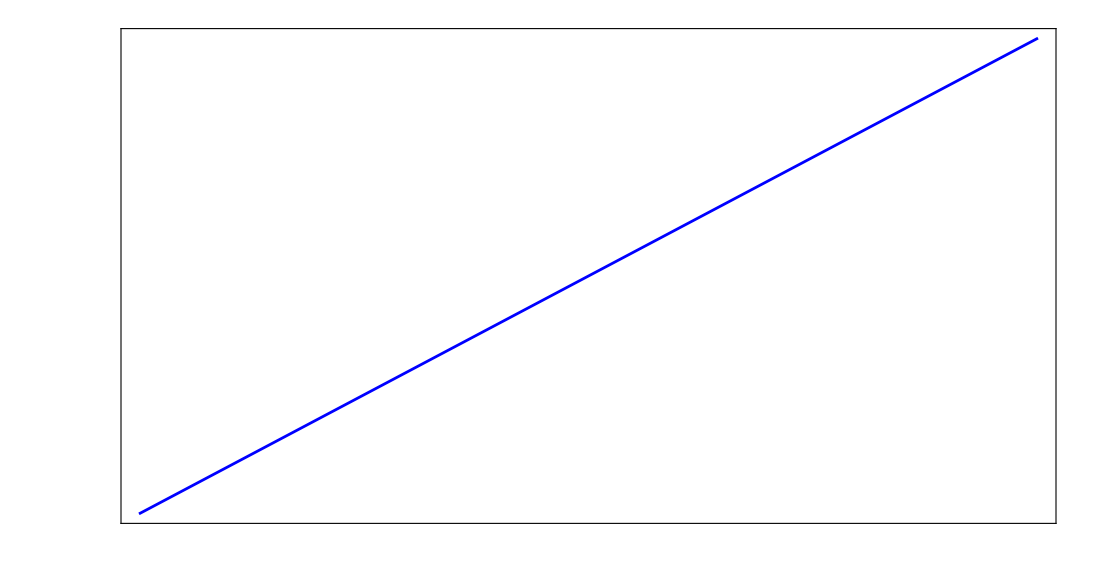
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-

```mathematica
spectrumPlots = sweepPanels[sweepData,deltaUsed,sweepGroups,sweepUsed,
 "Energies","E","\\text{Sector energy spectrum}"];
(* Inspect one plot before export. *)
spectrumPlots[[1]]
```

### 4.5 Half-chain eigenstate entropy

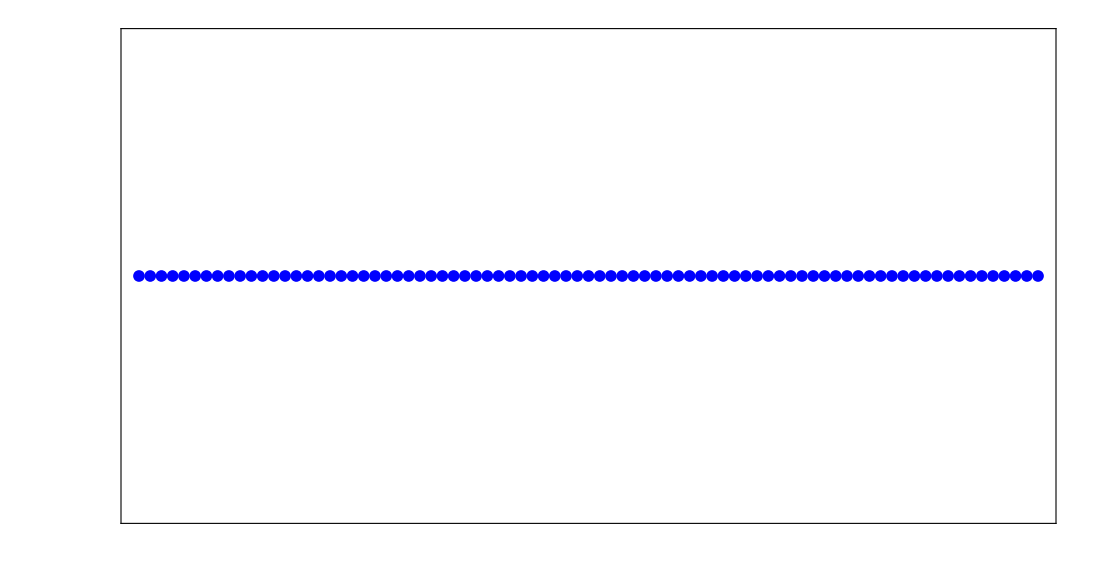
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-

```mathematica
halfPlots = sweepPanels[sweepData,deltaUsed,sweepGroups,sweepUsed,
 "HalfEntropy","S_{\\mathrm{half}}\\;(\\mathrm{nats})","\\text{Half-chain eigenstate entanglement}"];
halfPlots[[1]]
```

### 4.6 Edges-versus-middle eigenstate entropy

```mathematica
edgeEntropyPlots = sweepPanels[sweepData,deltaUsed,sweepGroups,sweepUsed,
 "EdgesEntropy","S_{AB|E}\\;(\\mathrm{nats})","\\text{Edges versus middle eigenstate entanglement}"];
edgeEntropyPlots[[1]]
```

-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-

### 4.7 Export sweep plots and data

```mathematica
sweepDir = newFolder[outputRoot,sweepLabel<>"_L"<>ToString[sweepUsed["L"]]<>
 "_J"<>safeToken[sweepUsed["J"]]];
Do[savePNG[FileNameJoin[{sweepDir,"spectrum_group_"<>ToString[k]<>".png"}],spectrumPlots[[k ]]],
 {k,Length[spectrumPlots]}];
Do[savePNG[FileNameJoin[{sweepDir,"half_entropy_group_"<>ToString[k]<>".png"}],halfPlots[[k ]]],
 {k,Length[halfPlots]}];
Do[savePNG[FileNameJoin[{sweepDir,"edge_entropy_group_"<>ToString[k]<>".png"}],edgeEntropyPlots[[k ]]],
 {k,Length[edgeEntropyPlots]}];
Export[FileNameJoin[{sweepDir,"eigenstate_sweep.wxf"}],
 <|"Model"->sweepUsed,"DeltaGrid"->deltaUsed,"Groups"->sweepGroups,"Data"->sweepData|>,"WXF"];
Print["Saved: ",sweepDir];
```

Saved: C:\Users\Miguel\Documents\GitHub\Spin-transport\xxz_impurities_characterization\xxz_open_edges_results\sweep01_fieldLeft_0.1_L8_J1

## 5. Evolution: independent parameters and diagonalization

### 5.1 Choose the Hamiltonian for this evolution

Set all evolution parameters here, including Delta. Running the sweep is unnecessary.

```mathematica
evoModel = <|
 "L" -> 8,
 "J" -> 1,
 "Delta" -> 0.5,
 "h" -> 0,
 "bLeft" -> 0.01,
 "bRight" -> 0
|>;
evoLabel = "evolution01_fieldLeft_0.01";
```

### 5.2 Choose the evolution time grid

```mathematica
evoTime = <|
 "Grid" -> "Linear",
 "tMax" -> 400.,
 "dt" -> 0.1,
 "tMinPositive" -> 0.01,
 "LogPoints" -> 501
|>;
```

### 5.3 Diagonalize this Hamiltonian

```mathematica
evoUsed = evoModel;
{evoEDSeconds,evoED} = AbsoluteTiming[sectorED[evoUsed,edTolerance ]];
evoSectors = sectorTable[evoED];
Print["ED seconds: ",evoEDSeconds,"; tolerance: ",edTolerance];
Dataset[evoSectors]
```

ED seconds: 0.0281346; tolerance: 1/10000000000

### 5.4 Optional fixed-Delta eigenstate plots

```mathematica
evoEigenstates = addEntropies[evoED];
evoEnergies = Lookup[evoEigenstates["Sectors"],"Eigenvalues"];
evoGroups = Gather[Range[Length[evoEnergies ]],
 Length[evoEnergies[[#1 ]]]==Length[evoEnergies[[#2 ]]] &&
 maxAbs[evoEnergies[[#1 ]]-evoEnergies[[#2 ]]]<matchingTolerance Max[1.,maxAbs[evoEnergies ]]&];
```

```mathematica
fixedEnergyPlots = fixedPanels[evoEigenstates,evoGroups,"Eigenvalues","E_n","\\text{Sector energies}"];
fixedHalfPlots = fixedPanels[evoEigenstates,evoGroups,"HalfEntropy",
 "S_{\\mathrm{half}}\\;(\\mathrm{nats})","\\text{Half-chain eigenstate entanglement}"];
fixedEdgePlots = fixedPanels[evoEigenstates,evoGroups,"EdgesEntropy",
 "S_{AB|E}\\;(\\mathrm{nats})","\\text{Edges versus middle eigenstate entanglement}"];
```

## 6. Initial states for this evolution

### 6.1 Choose factorized or full-chain mode

```mathematica
stateMode = "Factorized";   (* Factorized or Full *)
```

```mathematica
stateMode = "Full";   (* Factorized or Full *)
```

### 6.2 State of the two edge spins

Basis {00,01,10,11}. Enter a four-component vector or a 4*4 density matrix. Used only in Factorized mode.

```mathematica
(*edgeState = {1,1,1,1}/2;*)
(* Alternatives: {0,1,1,0}/Sqrt[2], {0,0,1,0}, IdentityMatrix[4]/4. *)
```

```mathematica
Flatten[KroneckerProduct[{0,1},{1,0}]]+Flatten[KroneckerProduct[{1,0},{0,1}]]
```

{0,1,1,0}

```mathematica
edgeState = {0,1,1,0}/Sqrt[2];
```

```mathematica
edgeState={1,1,1,1}/2;
```

### 6.3 State of the middle spins

Dimension 2^(L−2), physical order {2,…,L−1}. neel[n,0] starts with up on physical site 2; neel[n,1] starts with down. A middle helix starts its phase at physical site 2.

```mathematica
(*middleState = neel[evoModel["L"]-2,0];*)
(* Alternatives: 
productKet[ConstantArray[{1,0},evoModel["L"]-2]],
   helix[evoModel["L"]-2,Pi/3], or your vector/density matrix. *)
```

```mathematica
middleState = productKet[ConstantArray[{1,0},evoModel["L"]-2]];
```

```mathematica
ConstantArray[{1,0},evoModel["L"]-2]
```

{{1,0},{1,0},{1,0},{1,0}}

```mathematica
middleState = productKet[ConstantArray[{1,1},evoModel["L"]-2]]
```

{0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25}

```mathematica
middleState = neel[evoModel["L"]-2,0]
```

{0.,0.,0.,0.,0.,1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

### 6.4 Full initial state

Used only in Full mode. Enter a full-chain vector/density matrix in site order {1,…,L}, or select an eigenvector using evoSectors. A single eigenvector gives stationary reduced observables.

```mathematica
fullState = groundKet[evoED];
(* Alternatives: eigenket[evoED,3,1], neel[evoModel["L"]],
   helix[evoModel["L"],Pi/3], or your full-chain state. *)
```

```mathematica
fullState=eigenket[evoED,3,1];
```

### 6.5 Assemble and inspect the initial state

```mathematica
check[evoUsed===evoModel,"Evolution parameters changed: rerun section 5.3."];
check[MemberQ[{"Factorized","Full"},stateMode],"Invalid stateMode."];
If[stateMode=="Factorized",
 edgeFactor = stateFactor[edgeState,4,validationTolerance];
 middleFactor = stateFactor[middleState,2^(evoUsed["L"]-2),validationTolerance];
 fullFactor = joinStates[edgeFactor,middleFactor,evoUsed["L"]],
 fullFactor = stateFactor[fullState,2^evoUsed["L"],validationTolerance]
];
rhoEdge0 = reducedState[fullFactor,{1,evoUsed["L"]},evoUsed["L"]];
MatrixForm[rhoEdge0]
```

(0. | 0. | 0. | 0.
0. | 0.5 | 0.5 | 0.
0. | 0.5 | 0.5 | 0.
0. | 0. | 0. | 0.)

### 6.6 Prepare the evolution coefficients

```mathematica
engine = makeEngine[evoED,fullFactor];
Print["Occupied sectors: ",Length[engine["Sectors"]],
 "; initial factor columns: ",engine["Columns"]];
```

Occupied sectors: 1; initial factor columns: 1

## 7. Evolution, observables, and exports

### 7.1 Generate the time grid

```mathematica
evoTimeUsed = evoTime;
times = timeGrid[evoTimeUsed];
Print["Time points: ",Length[times],"; last time: ",Last[times ]];
```

Time points: 4001; last time: 400.

### 7.2 Evolve and calculate edge observables

```mathematica
check[evoUsed===evoModel,"Evolution parameters changed: rerun section 5.3 onward."];
check[engine["Parameters"]===evoUsed,"Engine belongs to another Hamiltonian: rerun section 6.6."];
{evolutionSeconds,evoData} = AbsoluteTiming[
 evolveChunks[times,engine,rhoEdge0,validationTolerance,parallel ]];
Print["Evolution seconds: ",evolutionSeconds];
```

Available parallel kernels: 12

Time batches: 32; maximum points per batch: 128

Evolution seconds: 0.886785

### 7.3 Numerical checks

```mathematica
evoChecks = <|
 "InitialFactorError" -> Norm[evolve[0.,engine]-fullFactor,"Frobenius"],
 "InitialEdgeError" -> Norm[First[evoData]["RhoAB"]-rhoEdge0,"Frobenius"],
 "MaxTraceError" -> Max[Lookup[evoData,"TraceError"]],
 "MaxHermiticityError" -> Max[Lookup[evoData,"HermiticityError"]],
 "MinEigenvalue" -> Min[Lookup[evoData,"MinEigenvalue"]]
|>;
check[Max[Values[KeyDrop[evoChecks,"MinEigenvalue"]]]<validationTolerance &&
 evoChecks["MinEigenvalue"]>=-validationTolerance,"Evolution validation failed."];
evoChecks
```

<|InitialFactorError→6.12198×10^-16,InitialEdgeError→5.46721×10^-16,MaxTraceError→8.88178×10^-16,MaxHermiticityError→0.,MinEigenvalue→-2.77556×10^-16|>

### 7.4 Build and inspect the plots

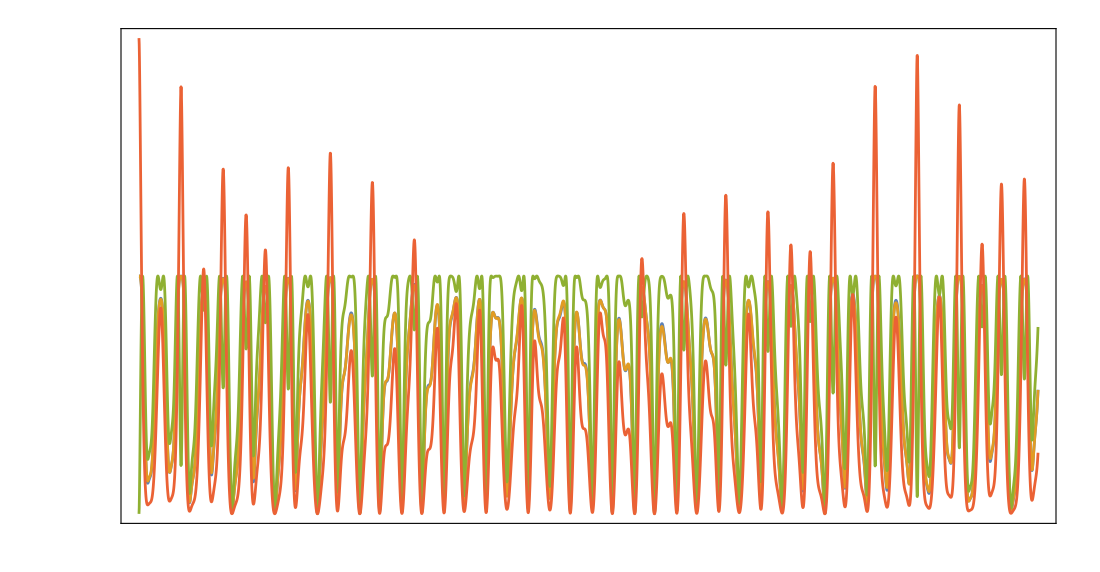
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-

```mathematica
evoPlots = densityPanels[evoData,evoUsed,evoTimeUsed];
If[TrueQ[exportLogTime],evoPlots=Join[evoPlots,densityPanels[evoData,evoUsed,evoTimeUsed,True ]]];
evoPlots["03_entropies_mutual_information"]
```

### 7.5 Export plots

```mathematica
evoDir = newFolder[outputRoot,evoLabel<>"_L"<>ToString[evoUsed["L"]]<>
 "_J"<>safeToken[evoUsed["J"]]<>"_Delta"<>safeToken[evoUsed["Delta"]]];
Do[savePNG[FileNameJoin[{evoDir,key<>".png"}],evoPlots[key ]],{key,Keys[evoPlots]}];
Print["Saved: ",evoDir];
```

Saved: C:\Users\Miguel\Documents\GitHub\Spin-transport\xxz_impurities_characterization\xxz_open_edges_results\evolution01_fieldLeft_0.01_L8_J1_Delta0p5

### 7.6 Export initial states, eigenpairs, and numerical data

```mathematica
Export[FileNameJoin[{evoDir,"initial_state.wxf"}],
 <|"Mode"->stateMode,"FullFactor"->fullFactor,"RhoAB0"->rhoEdge0|>,"WXF"];
Export[FileNameJoin[{evoDir,"sector_eigenpairs.wxf"}],evoED,"WXF"];
Export[FileNameJoin[{evoDir,"edge_dynamics.wxf"}],
 <|"Model"->evoUsed,"TimeSettings"->evoTimeUsed,"Checks"->evoChecks,"Data"->evoData|>,"WXF"];
Export[FileNameJoin[{evoDir,"parameters.txt"}],ToString[
 <|"Model"->evoUsed,"TimeSettings"->evoTimeUsed,"TimeGrid"->times,"StateMode"->stateMode,
 "EDTolerance"->edTolerance,"ValidationTolerance"->validationTolerance,"Parallel"->parallel,
 "EDSeconds"->evoEDSeconds,"EvolutionSeconds"->evolutionSeconds,"Checks"->evoChecks,
 "Notes"->"Raw energy eigenvectors; entropy in nats; Pauli magnetization. Ground-state ties follow sector order. Reduced entropy is bipartite entanglement only for a pure full state."|>,InputForm],"Text"];
```

### 7.7 Optional export of fixed-Delta eigenstate plots

```mathematica
If[ValueQ[evoEigenstates] && evoEigenstates["Parameters"]===evoUsed && ValueQ[fixedEnergyPlots],
 Do[savePNG[FileNameJoin[{evoDir,"fixed_energy_group_"<>ToString[k]<>".png"}],fixedEnergyPlots[[k ]]],
  {k,Length[fixedEnergyPlots]}];
 Do[savePNG[FileNameJoin[{evoDir,"fixed_half_group_"<>ToString[k]<>".png"}],fixedHalfPlots[[k ]]],
  {k,Length[fixedHalfPlots]}];
 Do[savePNG[FileNameJoin[{evoDir,"fixed_edges_group_"<>ToString[k]<>".png"}],fixedEdgePlots[[k ]]],
  {k,Length[fixedEdgePlots]}]
];
```

## 8. Access and modify results

For another initial state at the same Hamiltonian, edit section 6 and rerun 6.5–7. For another Hamiltonian, edit 5.1 and rerun 5.3 onward. The sweep can be skipped entirely. Exact degenerate eigenstate entropies remain basis dependent. S(rhoAB) measures edges–middle entanglement only when the full state is pure.

```mathematica
(* Evaluate any of these expressions individually. *)
(* eigenket[evoED,3,1] *)
(* evoED["Sectors"][[3]]["Eigenvalues"] *)
(* evoData[[10]]["RhoAB"] // MatrixForm *)
(* evoData[[10]]["RhoA"] // MatrixForm *)
(* evoData[[10]]["RhoB"] // MatrixForm *)
(* reducedState[evolve[1.,engine],{1,evoUsed["L"]},evoUsed["L"]] *)
```

## 9. Delta sweep of edge dynamics

### 9.1 Physics definitions

```mathematica
If[Length[DownValues[sectorED]]==0 || Length[DownValues[evolveChunks]]==0 ||
 Length[DownValues[framePlot]]==0,
 Print["Evaluate definitions 1-2 of xxz_open_edges_revised.m first."];Abort[]];
ClearAll[fullOverlapBatch,extraRecords,deltaColor,deltaBar,deltaPanel];
```

```mathematica
(*Entropies use natural logarithms. For a pure full state, S_A, S_B and S_AB measure
A versus the rest, B versus the rest, and both edges versus the middle.
Local expectations and correlations use Pauli matrices: sigma=2 S.
Full survival is |<psi(0)|psi(t)>|^2. Mixed inputs use the normalized
full-state overlap Tr[rho(0)rho(t)]/Tr[rho(0)^2] instead.*)
```

### Spectral overlap; no full - state evolution is repeated .

```mathematica
fullOverlapBatch[ts_List,eng_,purity0_] := Module[
 {out=ConstantArray[0.,Length[ts]],rank=eng["Columns"],amp,ph},
 Do[amp=ConstantArray[0.+0.I,Length[ts]];
  Do[ph=Exp[-I Outer[Times,s["E"],N[ts]]];
   amp+=(Conjugate[s["C"][[All,i]]] s["C"][[All,j]]) . ph,
   {s,eng["Sectors"]}];
  out+=Abs[amp]^2,{i,rank},{j,rank}];
 Developer`ToPackedArray[Re[out]/purity0]
];
```

### Add local Pauli expectations, pair correlations and full overlap .

```mathematica
extraRecords[records_List,eng_,purity0_] := Module[
 {overlap,pauli=PauliMatrix /@ Range[3],axes={"X","Y","Z"}},
 overlap=fullOverlapBatch[Lookup[records,"Time"],eng,purity0];
 MapThread[Function[{rec,ov},Module[{ra=rec["RhoA"],rb=rec["RhoB"],
   r=rec["RhoAB"],a,b,c,extra},
  a=Re[Tr[# . ra]]& /@ pauli;b=Re[Tr[# . rb]]& /@ pauli;
  c=Table[Re[Tr[KroneckerProduct[pauli[[i]],pauli[[j]]] . r]],{i,3},{j,3}];
  extra=Association[Join[
   {"PurityA"->Re[Tr[ra . ra]],"PurityB"->Re[Tr[rb . rb]],"FullOverlap"->ov},
   Table["LocalA"<>axes[[i]]->a[[i]],{i,3}],
   Table["LocalB"<>axes[[i]]->b[[i]],{i,3}],
   Flatten[Table[{
    "Correlation"<>axes[[i]]<>axes[[j]]->c[[i,j]],
    "Connected"<>axes[[i]]<>axes[[j]]->(c[[i,j]]-a[[i]] b[[j]])},
    {i,3},{j,3}],2]]];
  KeyDrop[Join[rec,extra],{"RhoAB","RhoA","RhoB","EigenvaluesAB"}]
 ]],{records,overlap}]
];
```

### 9.2 Plot definitions and labels

```mathematica
(*Red for negative Delta, purple at zero, blue for positive Delta. *)
deltaColor[d_,range_List] := Which[
 TrueQ[d==0],RGBColor[.5,0,.5],
 d<0,Blend[{Red,RGBColor[.5,0,.5]},Clip[Rescale[d,{Min[First[range],0],0}],{0,1}]],
 True,Blend[{RGBColor[.5,0,.5],Blue},Clip[Rescale[d,{0,Max[Last[range],0]}],{0,1}]]
];
```

```mathematica
(*Explicit ticks include zero; curves and colorbar share the same mapping. *)
deltaBar[range_List] := Module[{v,marks},
 v=N[Subdivide[First[range],Last[range],256]];
 marks=Sort[DeleteDuplicates[Join[N[Subdivide[First[range],Last[range],4]],
  If[First[range]<=0<=Last[range],{0.},{}]],Abs[#1-#2]<10^-12&]];
 Column[{tex["\\Delta",18],
  Graphics[{Raster[Table[{List@@deltaColor[Mean[v[[{k,k+1}]]],range]},
    {k,Length[v]-1}],{{0,First[range]},{1,Last[range]}}]},
   Frame->True,Axes->False,FrameStyle->Black,
   FrameTicks->{{None,({#,tex[texNumber[#],13]}& /@ marks)},{None,None}},
   PlotRange->{{0,1},range},PlotRangePadding->None,
   ImagePadding->{{5,70},{8,8}},ImageSize->{130,350},
   AspectRatio->Full,Background->White]},Alignment->Center,Spacings->.3]
];
```

```mathematica
(*One observable per panel, with Delta encoded by curve color. *)
deltaPanel[results_,ts_,p_,time_,spec_,log_:False] := Module[
 {range,curves,styles,note,g},
 range=MinMax[Lookup[results,"Delta"]];
 curves=Table[Transpose[{ts,r["Values"][spec[[1]]]}],{r,results}];
 If[log,curves=Select[#,First[#]>0&]& /@ curves];
 styles=(Directive[deltaColor[#["Delta"],range],AbsoluteThickness[2]]& /@ results);
 note="t\\in[0,"<>texNumber[time["tMax"]]<>"];\\quad N_t="<>ToString[Length[ts]]<>
  If[time["Grid"]=="Linear",";\\quad \\delta t="<>texNumber[time["dt"]],
   ";\\quad \\text{logarithmic sampling}"];
 g=Legended[framePlot[curves,"t\\quad(\\hbar=1)",spec[[3]],styles,{},True,log],
  Placed[deltaBar[range],Right]];
 plotPanel[spec[[2]],caption[p,
  "\\Delta\\in["<>texNumber[First[range]]<>","<>texNumber[Last[range]]<>
  "];\\quad N_\\Delta="<>ToString[Length[results]],note],g]
];
```

```mathematica
(*{data key, title, y label}; each entry creates its own PNG. *)
dynPlotSpecs={
 {"EntropyA","\\text{Entropy of edge A}","S(\\rho_A)\\quad(\\mathrm{nats})"},
 {"EntropyB","\\text{Entropy of edge B}","S(\\rho_B)\\quad(\\mathrm{nats})"},
 {"EntropyAB","\\text{Entropy of both edges}","S(\\rho_{AB})\\quad(\\mathrm{nats})"},
 {"MutualInfo","\\text{Edge mutual information}","I(A:B)\\quad(\\mathrm{nats})"},
 {"Concurrence","\\text{Edge concurrence}","C(\\rho_{AB})"},
 {"Negativity","\\text{Edge negativity}","\\mathcal N(\\rho_{AB})"},
 {"PurityA","\\text{Purity of edge A}","\\operatorname{Tr}[\\rho_A^2]"},
 {"PurityB","\\text{Purity of edge B}","\\operatorname{Tr}[\\rho_B^2]"},
 {"Purity","\\text{Purity of both edges}","\\operatorname{Tr}[\\rho_{AB}^2]"},
 {"FullOverlap","\\text{Full-state survival probability}","|\\langle\\psi(0)|\\psi(t)\\rangle|^2"},
 {"InitialOverlap","\\text{Initial reduced-edge overlap}",
  "\\operatorname{Tr}[\\rho_{AB}(0)\\rho_{AB}(t)]"}
};
dynAxes={"X","Y","Z"};dynTexAxes={"x","y","z"};
dynPlotSpecs=Join[dynPlotSpecs,
 Flatten[Table[
  {"Local"<>edge<>dynAxes[[i]],"\\text{Local expectation: edge "<>edge<>", "<>dynTexAxes[[i]]<>"}",
   "\\langle\\sigma_"<>If[edge=="A","1","L"]<>"^{"<>dynTexAxes[[i]]<>"}\\rangle"},
  {edge,{"A","B"}},{i,3}],1],
 Flatten[Table[
  {"Correlation"<>dynAxes[[i]]<>dynAxes[[j]],
   "\\text{Edge correlation: }"<>dynTexAxes[[i]]<>dynTexAxes[[j]],
   "\\langle\\sigma_1^{"<>dynTexAxes[[i]]<>"}\\sigma_L^{"<>dynTexAxes[[j]]<>"}\\rangle"},
  {i,3},{j,3}],1],
 Flatten[Table[
  {"Connected"<>dynAxes[[i]]<>dynAxes[[j]],
   "\\text{Connected edge correlation: }"<>dynTexAxes[[i]]<>dynTexAxes[[j]],
   "\\langle\\sigma_1^{"<>dynTexAxes[[i]]<>"}\\sigma_L^{"<>dynTexAxes[[j]]<>"}\\rangle_c"},
  {i,3},{j,3}],1]
];
```

### 9.3 Choose fixed parameters and the Delta sweep

```mathematica
dynModel=<|
 "L"->6,
 "J"->1,
 "h"->0,
 "bLeft"->0,
 "bRight"->0
|>;
dynDelta=N[Range[-0.5,0.5,0.1]];             (* Edit this list to change the sweep. *)
dynRunLabel="delta_dynamics";
```

```mathematica
dynTime=<|
 "Grid"->"Linear",
 "tMax"->50.,
 "dt"->0.1,
 "tMinPositive"->0.01,
 "LogPoints"->501
|>;
dynParallel=<|"Enabled"->True,"Kernels"->12,
 "MemoryBudgetGB"->15.,"BatchTimes"->128|>;
dynEDTolerance=10^-10;
dynValidationTolerance=10^-8;
```

```mathematica
plotChop=10^-10;
dynExportLogTime=False;
dynOutputRoot=FileNameJoin[{baseFolder[],"xxz_open_edges_delta_dynamics"}];
```

### 9.4 Choose the fixed initial state

```mathematica
dynStateMode="Factorized";             (* Factorized or Full. *)
```

```mathematica
dynEdgeState={0,0,1,0};                (* Basis {00,01,10,11}. *)
dynMiddleState=productKet[ConstantArray[{1,0},dynModel["L"]-2]];
(* Alternatives: neel[dynModel["L"]-2,0] or helix[dynModel["L"]-2,q]. *)
```

```mathematica
(*Full mode: enter one fixed vector or density matrix in site order 1,...,L. *)
dynFullState=productKet[ConstantArray[{1,0},dynModel["L"]]];
(* Example: dynFullState=eigenket[evoED,sector,level]; evaluate once before the sweep. *)
```

### 9.5 Prepare the fixed state and times

```mathematica
check[IntegerQ[dynModel["L"]] && dynModel["L"]>=3,"L must be an integer >=3."];
check[!KeyExistsQ[dynModel,"Delta"],"Put Delta values only in dynDelta."];
check[ListQ[dynDelta] && Length[dynDelta]>=2 && AllTrue[dynDelta,realQ] &&
 Length[DeleteDuplicates[N[dynDelta],TrueQ[#1==#2]&]]==Length[dynDelta],
 "Use at least two distinct real Delta values."];
check[MemberQ[{"Factorized","Full"},dynStateMode],"Invalid dynStateMode."];
dynModelUsed=dynModel;dynDeltaUsed=Sort[N[dynDelta]];
dynTimeUsed=dynTime;dynParallelUsed=dynParallel;
dynEDToleranceUsed=dynEDTolerance;dynValidationToleranceUsed=dynValidationTolerance;
dynTimes=timeGrid[dynTimeUsed];
```

```mathematica
If[dynStateMode=="Factorized",
 dynEdgeFactor=stateFactor[dynEdgeState,4,dynValidationToleranceUsed];
 dynMiddleFactor=stateFactor[dynMiddleState,2^(dynModelUsed["L"]-2),dynValidationToleranceUsed];
 dynFactor=joinStates[dynEdgeFactor,dynMiddleFactor,dynModelUsed["L"]],
 dynFactor=stateFactor[dynFullState,2^dynModelUsed["L"],dynValidationToleranceUsed]
];
dynRhoEdge0=reducedState[dynFactor,{1,dynModelUsed["L"]},dynModelUsed["L"]];
dynGram=ConjugateTranspose[dynFactor] . dynFactor;
dynPurity0=Re[Tr[dynGram . dynGram]];
dynPureInput=Abs[dynPurity0-1.]<=dynValidationToleranceUsed;
dynSpecsUsed=dynPlotSpecs;
If[!dynPureInput,
 dynSpecsUsed=Replace[dynSpecsUsed,
  {"FullOverlap",_,_}->{"FullOverlap","\\text{Normalized full-state overlap}",
   "\\operatorname{Tr}[\\rho(0)\\rho(t)]/\\operatorname{Tr}[\\rho(0)^2]"},1]];
Print["Fixed initial purity: ",dynPurity0,"; Delta points: ",Length[dynDeltaUsed],
 "; time points: ",Length[dynTimes]];
```

Fixed initial purity: 1.; Delta points: 11; time points: 501

### 9.6 Independent sector ED and evolution at every Delta

```mathematica
(*Delta values are processed in order; time batches use the existing parallel kernels.
Every symmetry sector is diagonalized independently, including special Delta=+/-1.
The full initial factor is reused at every Delta.*)
```

```mathematica
Clear[dynResults,dynPlots,dynLogPlots];
{dynSweepSeconds,dynResults}=AbsoluteTiming[
 Table[
  delta=dynDeltaUsed[[k]];
  Print["Delta = ",delta," (",k,"/",Length[dynDeltaUsed],")"];
  dynCurrentModel=Join[dynModelUsed,<|"Delta"->delta|>];
  {dynEDSeconds,dynCurrentED}=AbsoluteTiming[sectorED[dynCurrentModel,dynEDToleranceUsed]];
  dynCurrentEngine=makeEngine[dynCurrentED,dynFactor];
  {dynEvolutionSeconds,dynRecords}=AbsoluteTiming[
   evolveChunks[dynTimes,dynCurrentEngine,dynRhoEdge0,dynValidationToleranceUsed,dynParallelUsed]];
  dynRecords=extraRecords[dynRecords,dynCurrentEngine,dynPurity0];
  dynValues=Association[Table[
   key->Developer`ToPackedArray[N[Lookup[dynRecords,key]]],
   {key,DeleteCases[Keys[First[dynRecords]],"Time"]}]];
  Print["ED seconds: ",dynEDSeconds,"; evolution seconds: ",dynEvolutionSeconds];
  <|"Delta"->delta,"EDSeconds"->dynEDSeconds,"EvolutionSeconds"->dynEvolutionSeconds,
   "Sectors"->sectorTable[dynCurrentED],"Values"->dynValues|>,
  {k,Length[dynDeltaUsed]}]
];
Clear[dynCurrentED,dynCurrentEngine,dynRecords,dynValues];
Print["Delta sweep seconds: ",dynSweepSeconds];
```

Delta = -0.5 (1/11)

Available parallel kernels: 12

Time batches: 4; maximum points per batch: 128

ED seconds: 0.0109256; evolution seconds: 0.252524

Delta = -0.4 (2/11)

Available parallel kernels: 12

Time batches: 4; maximum points per batch: 128

ED seconds: 0.0123635; evolution seconds: 0.249404

Delta = -0.3 (3/11)

Available parallel kernels: 12

Time batches: 4; maximum points per batch: 128

ED seconds: 0.011148; evolution seconds: 0.26056

Delta = -0.2 (4/11)

Available parallel kernels: 12

Time batches: 4; maximum points per batch: 128

ED seconds: 0.0109341; evolution seconds: 0.252355

Delta = -0.1 (5/11)

Available parallel kernels: 12

Time batches: 4; maximum points per batch: 128

ED seconds: 0.0138407; evolution seconds: 0.247538

Delta = 0. (6/11)

Available parallel kernels: 12

Time batches: 4; maximum points per batch: 128

ED seconds: 0.0108281; evolution seconds: 0.256271

Delta = 0.1 (7/11)

Available parallel kernels: 12

Time batches: 4; maximum points per batch: 128

ED seconds: 0.0107215; evolution seconds: 0.272866

Delta = 0.2 (8/11)

Available parallel kernels: 12

Time batches: 4; maximum points per batch: 128

ED seconds: 0.0102687; evolution seconds: 0.252075

Delta = 0.3 (9/11)

Available parallel kernels: 12

Time batches: 4; maximum points per batch: 128

ED seconds: 0.0112726; evolution seconds: 0.284032

Delta = 0.4 (10/11)

Available parallel kernels: 12

Time batches: 4; maximum points per batch: 128

ED seconds: 0.0112509; evolution seconds: 0.238459

Delta = 0.5 (11/11)

Available parallel kernels: 12

Time batches: 4; maximum points per batch: 128

ED seconds: 0.0115629; evolution seconds: 0.250615

Delta sweep seconds: 3.96896

### 9.7 Individual plots

```mathematica
check[Length[dynResults]==Length[dynDeltaUsed] &&
 Lookup[dynResults,"Delta"]===dynDeltaUsed,"Incomplete Delta sweep."];
dynPlots=Association[Table[
 spec[[1]]->deltaPanel[dynResults,dynTimes,dynModelUsed,dynTimeUsed,spec],
 {spec,dynSpecsUsed}]];
Print["Individual linear-time plots: ",Length[dynPlots]];
```

Individual linear-time plots: 35

```mathematica
(*dynLogPlots=If[TrueQ[dynExportLogTime],
 Association[Table[
  spec[[1]]<>"_logtime"->deltaPanel[dynResults,dynTimes,dynModelUsed,dynTimeUsed,spec,True],
  {spec,dynSpecsUsed}]],<||>];*)
(* Display individually: dynPlots["EntropyAB"] or dynPlots["Concurrence"]. *)
```

### 9.8 PNG export and data

```mathematica
dynDir=newFolder[dynOutputRoot,dynRunLabel<>"_L"<>ToString[dynModelUsed["L"]]<>
 "_J"<>safeToken[dynModelUsed["J"]]<> "_h"<>safeToken[dynModelUsed["h"]]<>
 "_bL"<>safeToken[dynModelUsed["bLeft"]]<> "_bR"<>safeToken[dynModelUsed["bRight"]]<>
 "_Delta"<>safeToken[First[dynDeltaUsed]]<>"to"<>safeToken[Last[dynDeltaUsed]]];
Do[savePNG[FileNameJoin[{dynDir,key<>".png"}],dynPlots[key]],{key,Keys[dynPlots]}];
(*Do[savePNG[FileNameJoin[{dynDir,key<>".png"}],dynLogPlots[key]],{key,Keys[dynLogPlots]}];*)
Print["Saved PNGs: ",dynDir];
```

Saved PNGs: C:\Users\Miguel\Documents\GitHub\Spin-transport\xxz_impurities_characterization\xxz_open_edges_delta_dynamics\delta_dynamics_L6_J1_h0_bL0_bR0_Deltam0p5to0p5_run2

```mathematica
Export[FileNameJoin[{dynDir,"delta_dynamics.wxf"}],
 <|"Model"->dynModelUsed,"Delta"->dynDeltaUsed,"TimeGrid"->dynTimeUsed,"Times"->dynTimes,
  "InitialFactor"->dynFactor,"InitialPurity"->dynPurity0,"Parallel"->dynParallelUsed,
  "EDTolerance"->dynEDToleranceUsed,"ValidationTolerance"->dynValidationToleranceUsed,
  "SweepSeconds"->dynSweepSeconds,"Results"->dynResults|>,"WXF"];
Export[FileNameJoin[{dynDir,"parameters.txt"}],
 StringRiffle[{
  "Model: "<>ToString[dynModelUsed,InputForm],
  "Delta values: "<>ToString[dynDeltaUsed,InputForm],
  "Time grid: "<>ToString[dynTimeUsed,InputForm],
  "Initial factor is fixed across Delta and stored in delta_dynamics.wxf.",
  "Entropies: natural logarithms. Local and pair operators: Pauli matrices.",
  "Connected ab = <sigma_1^a sigma_L^b>-<sigma_1^a><sigma_L^b>.",
  "Full survival for pure inputs; normalized full overlap for mixed inputs.",
  "InitialOverlap = Tr[rho_AB(0) rho_AB(t)].",
  "Colors: negative Delta red, zero purple, positive Delta blue."
 },"\n"],"Text"];
```